```mathematica
f[x_] = x^6 - 3x^5 - 9x^4 + 19x^3 + 12x^2 - 36x + 16
```

16-36 x+12 x^2+19 x^3-9 x^4-3 x^5+x^6

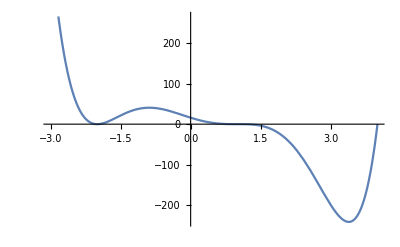

```mathematica
Plot[f[x],{x,-3,4}]
```

```mathematica
solutions=Solve[f[x]==0,x]
```

{{x→-2},{x→-2},{x→1},{x→1},{x→1},{x→4}}

```mathematica
solutions=NSolve[f[x]==0,x]
```

{{x→-2.},{x→-2.},{x→1.},{x→1.},{x→1.},{x→4.}}

```mathematica
solutions=Roots[f[x]==0,x]
```

x==-2||x==-2||x==1||x==1||x==1||x==4

```mathematica
solutions=FindRoot[f[x]==0,{x,-2}]
```

{x→-2.}

```mathematica
solutions=FindRoot[f[x]==0,{x,-1}]
```

{x→-2.}

```mathematica
solutions=FindRoot[f[x]==0,{x,1}]
```

{x→1.}

```mathematica
solutions=FindRoot[f[x]==0,{x,2}]
```

{x→1.}

```mathematica
solutions=FindRoot[f[x]==0,{x,3}]
```

{x→1.}

```mathematica
solutions=FindRoot[f[x]==0,{x,4}]
```

{x→4.}

```mathematica
Factor[f[x]]
```

(-4+x) (-1+x)^3 (2+x)^2